```mathematica
<< "/home/docencia/Documents/David/RRT/RandomData.m"
```

```mathematica
RandomData[]
```

0.773033

```mathematica
max=10000;
```

```mathematica
array=Table[RandomData[],{i,max}];(**)
```

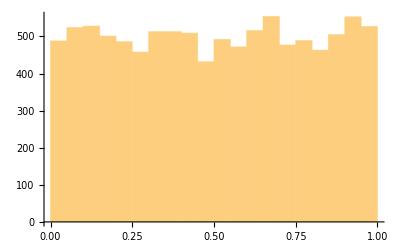

```mathematica
Histogram[array]
```

```mathematica
lambda=100;
```

```mathematica
arrayExp=Table[RandomExp[lambda],{i,max}];(*RandomExp es una funcion de Armando que ya tiene en cuenta lo de la dist uniforme*)
```

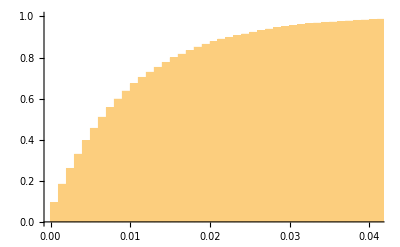

```mathematica
Histogram[arrayExp,l,CDF]
```

```mathematica
(*Para pedir ayuda de una funcion*)
?RandomData`*
```

```mathematica
(*Trunca un array entre 50 y 100*)
arrayExp[[50;;100]];
```

```mathematica
(*La media tiene que salir proxima a 1/lambda*)
mean=Mean[arrayExp[[1;;100]]]
```

0.00987223

```mathematica
InterArr=Table[RandomExp[lambda],10000];
```

```mathematica
InterArr[[1;;100]];
```

```mathematica
Arriv=Accumulate[InterArr];
```

{0.00188815,0.01252,0.0151322,0.0221056,0.0228372,0.0318143,0.036723,0.0497244,0.0532469,0.0556281,0.0569012}

```mathematica
mu=100;
ServTime=Table[RandomExp[mu],10000];
ServTime[[1;;11]]
```

{0.00944713,0.0188524,0.00774871,0.00100172,0.00118986,0.033824,0.00747578,0.00248454,0.00131683,0.00327753,0.00726003}

```mathematica
FifoSchedulling[arrivals_,service_]:=Module[{n,checkTime},n=1;checkTime=arrivals[[1]];
(If[checkTime≥#,checkTime+=service[[n++]],checkTime=#+service[[n++]]])&/@arrivals]
```

```mathematica
Departures=FifoSchedulling[Arriv,ServTime];
```

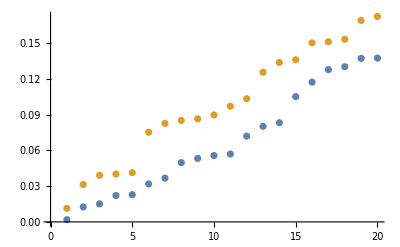

```mathematica
ListPlot[{Arriv[[1;;20]],Departures[[1;;20]]}]
```

```mathematica
(*Usar Map[] (sirve para recorrer una lista) en lugar de For[]*)
FifoSchedulling[arrivals_,service_]:=Module[{n,checkTime},n=1;checkTime=arrivals[[1]];
Map[
(If[checkTime≥#,checkTime+=service[[n++]],checkTime=#+service[[n++]]])&,
arrivals]]
```

```mathematica
(*MM/#colas/#usuarios: si hay dos colas y 3 usuarios, cada usuarios ira a una cola,y el tercero se queda esperando*)
```

```mathematica
Manipulate[
ListPlot[{Arriv[[origin;;origin+width]],Departures[[origin;;origin+width]]}]
, {origin,1,1000-width,1},{width,10,50,1}
]
```

```mathematica
(*Falta hacer la escalera*)
```